```mathematica
Clear[interPP,isumPP ,isumZP,isumZZ,isumWW,isumWWdyt]
SetDirectory[NotebookDirectory[]];
interPP = Get["intang_PPtt_10TeV_fix.txt"];
interZP = Get["intang_ZPtt_10TeV_fix.txt"];
```

```mathematica
interWW = Get["intang_WWtt1.txt"];
interZZ = Get["intang_ZZtt_10TeV_Fix.txt"];
```



```mathematica
(*benchmarklist={3,4,5,7,8,10,11};*)
ColorData[24,"Image"]
(*ColorData[109,"Image"]*)
colorselecitonumber=24;
```

```mathematica
energygrid=Grid[{Table[Style[If[j==1,{"(√s= 3,","6,","10,","14,","30,","100 TeV)"}[[i]],"TeV"],If[j≠0,ColorData[colorselecitonumber][i]],Bold],{j,1,2,1},{i,1,6,1}][[1]]},Spacings->{0.5,0}]
```

(√s= 3, | 6, | 10, | 14, | 30, | 100 TeV)

```mathematica
dytinterWW = Get["intang_WWttDYT_10TeV_3.txt"];
dytinterWW11= Get["intang_WWttDYT11_10TeV_3.txt"];
dytinterWWm1m1= Get["intang_WWttDYTm1m1_10TeV_3.txt"];
dytinterZZ = Get["intang_ZZtt00DYT_10TeV_3_new.txt"];
dytinterZZ11= Get["intang_ZZtt11DYT_10TeV_3.txt"];
dytinterZZm1m1= Get["intang_ZZttm1m1DYT_10TeV_3.txt"];
dytt = Table[(1/10000)*(30i-300),{i,0,20}]
```

{-3/100,-27/1000,-3/125,-21/1000,-9/500,-3/200,-3/250,-9/1000,-3/500,-3/1000,0,3/1000,3/500,9/1000,3/250,3/200,9/500,21/1000,3/125,27/1000,3/100}

```mathematica
dytt[[11]]
```

0

```mathematica
angenPP[ang_,num_] :=interPP[[ang]] [(1 + ((num - 350)/50))]

angenZP[ang_,num_] :=interZP[[ang]] [(1 + ((num - 350)/50))]

angenWW[ang_,num_] :=interWW[[ang]][(1 + ((num - 350)/50))]

angenZZ[ang_,num_] :=interZZ[[ang]][(1 + ((num - 350)/50))]
```

```mathematica
isumWWdyt[ang_,dyt_,energy_] :=dytinterWW[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdyt11[ang_,dyt_,energy_] :=dytinterWW11[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWW11[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumWWdytm1m1[ang_,dyt_,energy_] :=dytinterWWm1m1[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterWWm1m1[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdyt00[ang_,dyt_,energy_] :=dytinterZZ[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdyt11[ang_,dyt_,energy_] :=dytinterZZ11[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZ11[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
isumZZdytm1m1[ang_,dyt_,energy_] :=dytinterZZm1m1[[ang,dyt]][(1 + ((energy - 350)/50))]-dytinterZZm1m1[[ang,11]][(1 + ((energy - 350)/50))]
```

```mathematica
lum = 10;
sqrtsbin = Table[350 + 50*i, {i,0,194}];
br = 88.9;
```

0.888889

```mathematica
background = Table[NIntegrate[br*lum*(angenPP[k,ss]+angenWW[k,ss]+angenZP[k,ss]+angenZZ[k,ss]),{ss,sqrtsbin[[i]],sqrtsbin[[i+1]]}],{i,1,53},{k,1,18}];
```

```mathematica
signal = Table[NIntegrate[br*lum*(isumWWdyt[k,j,ss]+isumWWdyt11[k,j,ss]+isumWWdytm1m1[k,j,ss]+isumZZdyt00[k,j,ss]+isumZZdyt11[k,j,ss]+isumZZdytm1m1[k,j,ss]),{ss,sqrtsbin[[i]],sqrtsbin[[i+1]]}],{i,1,53},{k,1,18},{j,1,Length@dytt}]
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
(*Sum angles*)
sumanglesbkg = Table[Sum[background[[i,n]],{n,2,17}],{i,1,53}];
sumanglessig = Table[Sum[signal[[i,n,j]],{n,2,17}],{i,1,53},{j,1,Length@dytt}];
```

```mathematica
sqrtsumanglesbkg =Sqrt[sumanglesbkg];
```

```mathematica
background1 = Table[NIntegrate[br*lum*(angenPP[k,ss]+angenWW[k,ss]+angenZP[k,ss]+angenZZ[k,ss]),{ss,3000,10000}],{k,2,17}];
```

```mathematica
signal1 = Table[NIntegrate[br*lum*(isumWWdyt[k,j,ss]+isumWWdyt11[k,j,ss]+isumWWdytm1m1[k,j,ss]+isumZZdyt11[k,j,ss]+isumZZdytm1m1[k,j,ss]),{ss,3000,10000}],{k,2,17},{j,1,Length@dytt}];
```

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

```mathematica
(*Sum angles*)

sumanglesbkg1 = Sum[background1[[n]],{n,1,16}];
sumanglessig1 = Table[Sum[signal1[[n,j]],{n,1,16}],{j,1,Length@dytt}];
sqrtsumanglesbkg1 =Sqrt[sumanglesbkg1];
```

```mathematica
sumanglesbkg1
```

2696.51

```mathematica
zzzz = Sum[sumanglesbkg[[i]],{i,1,53}]+sumanglesbkg1
```

353290.

```mathematica
zzz
```

{31102.8+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,42949.4+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,41041.3+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,36660.5+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,31848.8+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,27372.9+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,23469.1+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,20166.2+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,17413.1+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,15133.1+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,13248.1+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,11687.5+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,10391.4+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,9310.6+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,8405.15+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,7642.87+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,6997.97+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,6449.71+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,5981.4+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,5579.57+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,5233.27+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,4933.58+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,4673.22+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,4446.16+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,4247.45+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,4072.95+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,3919.23+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,3783.39+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,3663.02+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,3556.05+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,3460.75+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,3375.63+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,3299.43+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,3231.06+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,3169.57+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,3114.17+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,3064.15+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,3018.9+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2977.9+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2940.69+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2906.85+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2876.03+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2847.93+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2822.26+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2798.78+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2777.27+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2757.54+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2739.43+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2722.78+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2707.46+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2693.33+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2680.3+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧,2668.27+{197.714,123.364,86.999,67.0173,55.984,51.0321,51.0554,55.842,65.8075,81.9764,106.156,141.436,193.484,274.24,414.714,729.691}⟦17⟧}

```mathematica
chi2sumang = Table[Sum[(sumanglessig [[i,j]]/sqrtsumanglesbkg [[i]])^2,{i,1,53}],{j,1,Length@dytt}];
```

```mathematica
chi2sumang1 = Table[(sumanglessig1 [[j]]/sqrtsumanglesbkg1)^2,{j,1,Length@dytt}];
```

```mathematica
chi = chi2sumang +chi2sumang1 ;
```

```mathematica
dytt = Table[(1/10000)*(30i-300),{i,0,20}]
dytchi2en = Table[{dytt[[k]],chi[[k]]},{k,1,Length@dytt}];
intdytchi2en = Interpolation[dytchi2en ]
sig1= Table[{dytt[[k]],1},{k,1,Length@dytt}];
```

{-3/100,-27/1000,-3/125,-21/1000,-9/500,-3/200,-3/250,-9/1000,-3/500,-3/1000,0,3/1000,3/500,9/1000,3/250,3/200,9/500,21/1000,3/125,27/1000,3/100}

InterpolatingFunction[…]

```mathematica
(*bin angle and energy*)
sqrtback = Sqrt[background];
chi2 = Table[Sum[(signal[[i,j,k]]/ sqrtback[[i,j]])^2,{i,1,33},{j,2,17}],{k,1,Length@dytt}];
```

```mathematica
dytchi2enang = Table[{dytt[[k]],chi2 [[k]]},{k,1,Length@dytt}];
intdytchi2enang = Interpolation[dytchi2enang ]
sig1= Table[{dytt[[k]],1},{k,1,Length@dytt}];
```

InterpolatingFunction[…]

```mathematica
dyttnew = Table[(1/10000)*(i-300),{i,0,600}];
```

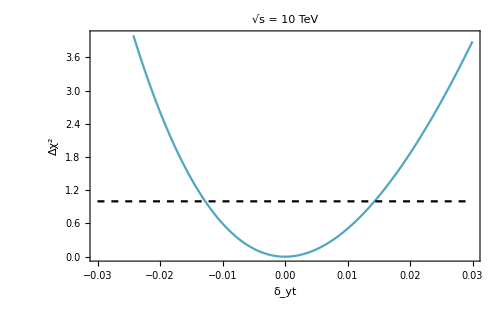

```mathematica
lineplot=ListPlot[{Transpose[{ dyttnew ,intdytchi2enang [dyttnew]}] ,sig1},Joined->True,PlotStyle->{ColorData[colorselecitonumber][5],{Dashed,Black}},Frame->True,FrameLabel->{Style[DisplayForm["δ_yt"],Black,20,FontFamily->"Times"],Style["Δχ^2",Black,19,FontFamily->"Times"]},
PlotLabel->Style[DisplayForm[SqrtBox["s"] ]  Row[{" = ",10 TeV}]  ,Black,18,FontFamily->"Times"],
PlotRange->{{-0.03,0.03},{0,4}},
FrameTicksStyle->Directive[Black,17],ImageSize->500]
```

```mathematica
Export["chi_square_10TeV_angle_dilepton_out.pdf",lineplot]
```

chi_square_10TeV_angle_dilepton_out.pdf